| Estimate | Standard Error | t-Statistic | P-Value
Ree | 36.1954 | 127.961 | 0.282862 | 0.779813
b | 16.3459 | 1.7515 | 9.33249 | 2.76875×10^-9
Ref | 7.7974×10^59 | 0. | ∞ | 0.

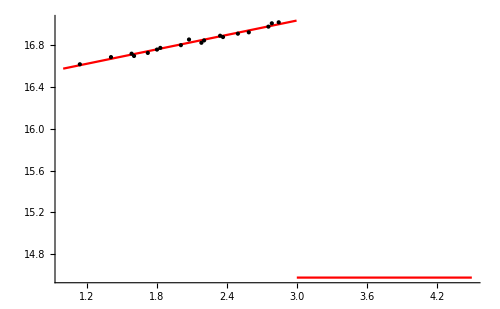

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["noyola_ready_0,25.dat"];
L=Length[data];
Ie=1000;
Ip[R_]:=Piecewise[{{(8.32678/Ree)*R+b,R<3},{Log[Ie*Exp[-7.669*((R/Ref)^0.25-1.0)]],R>3}}]
(*Plot[Log[Ip[R]],{R,0,12}]*)
fit = NonlinearModelFit[data,Ip[R],{Ree,b,Ref},R,MaxIterations->1000];
(*fit//Normal//InputForm*)
(*fit["BestFit"]*)
fit["ParameterTable"]
Plot[fit[R],{R,1,4.5},PlotStyle->Red,Epilog:>Point[data],ImageSize->500]
```